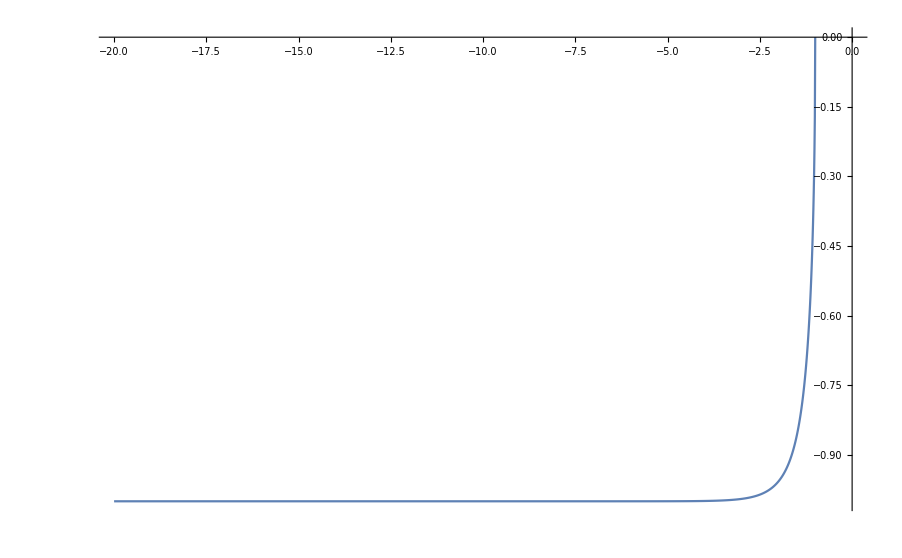

```mathematica
Clear["Global`*"]


a=ParallelTable[{r,x/. (NSolve[Exp[2 r x]==(1-x)/(1+x),x,Reals])[[1]]},{r,-1,-20,-0.01}];

ListPlot[a,Joined->True]
```